```mathematica
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]

Any quantum circuit:

```mathematica
circuit=QuantumCircuitOperator[{"BooleanOracleR",a&&!b||c}]
```

QuantumCircuitOperator[…]

Has a tensor network representation:

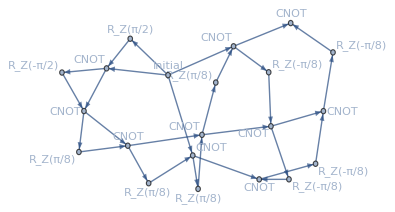

```mathematica
net=circuit["TensorNetwork"]
```

Which is just a graph annotated with tensors and contraction indices:

```mathematica
GraphQ[net]&&TensorNetworkQ[net]
```

True

```mathematica
EdgeList[net]
```

{01{0^4,1_4},02{0^3,2_3},12{1^4,2_4},23{2^4,3_4},24{2^3,4_3},34{3^4,4_4},45{4^4,5_4},46{4^3,6_3},56{5^4,6_4},67{6^4,7_4},08{0^2,8_2},78{7^4,8_4},89{8^4,9_4},610{6^3,10_3},910{9^4,10_4},1011{10^4,11_4},012{0^1,12_1},1112{11^4,12_4},1213{12^4,13_4},1014{10^3,14_3},1314{13^4,14_4},1415{14^4,15_4},816{8^2,16_2},1516{15^4,16_4},1617{16^4,17_4},1418{14^3,18_3},1718{17^4,18_4},1819{18^4,19_4},1220{12^1,20_1},1920{19^4,20_4}}

Vertices correspond to circuit’s operator indices + “Initial” tensor with index 0:

```mathematica
Length@circuit["Operators"]==Max[VertexList[net]]
```

True

(don’t mind the Developer`FromPackedArray, it’s a bug in AnnotationValue)

```mathematica
AnnotationValue[{net,Developer`FromPackedArray@RandomChoice[VertexList[net],3]},"Tensor"]
```

{SparseArray[…],SparseArray[…],SparseArray[…]}

```mathematica
AnnotationValue[{net,Developer`FromPackedArray@RandomChoice[VertexList[net],3]},"Index"]
```

{{0^1,0^2,0^3,0^4},{8^2,8^4,8_2,8_4},{11^4,11_4}}

Free indices are the ones that left after contraction:

```mathematica
TensorNetworkFreeIndices[net]
```

{20^1,16^2,18^3,20^4}

“Initial” vertex (index 0) is pre-initialized with 0000.. register tensor. To initialize with a different vector use InitializeTensorNetwork:

```mathematica
state=QuantumState[{"RandomPure",circuit["Width"]}];
```

```mathematica
net=InitializeTensorNetwork[net,state["Tensor"]];
```

Contraction is performed in the order of network’s EdgeList:

```mathematica
finalTensor=ContractTensorNetwork[net]
```

SparseArray[…]

Confirm that the result is the same as default circuit application:

```mathematica
circuit[state]["Tensor"]==finalTensor
```

True

Now with measurement:

```mathematica
measurement=QuantumMeasurementOperator[{3,1}][circuit][state]
```

QuantumMeasurement[…]

```mathematica
ContractTensorNetwork[InitializeTensorNetwork[QuantumMeasurementOperator[{3,1}][circuit]["TensorNetwork"],state["Tensor"]]]==measurement["Tensor"]
```

True

Another tensor network representation uses indices as graph vertices with tensors as cliques:

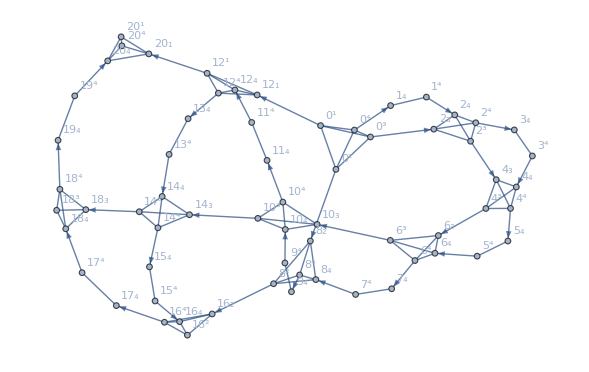

```mathematica
indexNet=TensorNetworkIndexGraph[net]
```

```mathematica
FindClique[indexNet,Infinity,All]
```

{{0^1,0^2,0^3,0^4},{20_1,20_4,20^1,20^4},{18_3,18_4,18^3,18^4},{16_2,16_4,16^2,16^4},{14_3,14_4,14^3,14^4},{12_1,12_4,12^1,12^4},{10_3,10_4,10^3,10^4},{8_2,8_4,8^2,8^4},{6_3,6_4,6^3,6^4},{4_3,4_4,4^3,4^4},{2_3,2_4,2^3,2^4},{19_4,19^4},{17_4,17^4},{15_4,15^4},{13_4,13^4},{11_4,11^4},{9_4,9^4},{7_4,7^4},{5_4,5^4},{3_4,3^4},{1_4,1^4}}

Free indices can be extracted as vertices with zero in- and out- degree:

```mathematica
Pick[VertexList[indexNet],VertexInDegree[indexNet]+VertexOutDegree[indexNet],0]
```

{16^2,18^3,20^1,20^4}

```mathematica
ContainsExactly[%,TensorNetworkFreeIndices[net]]
```

True

Thanks EinsteinSummation for speeding up the naive contraction!

```mathematica
ContractTensorNetwork[net]===ResourceFunction["EinsteinSummation"][
(AnnotationValue[{net,Developer`FromPackedArray@VertexList[net]},"Index"]/.Rule@@@EdgeTags[net])->TensorNetworkFreeIndices[net],AnnotationValue[{net,Developer`FromPackedArray@VertexList[net]},"Tensor"]
]
```

True

```mathematica
ContractTensorNetwork[net,Method->"Naive"];//RepeatedTiming
```

{0.0854574,Null}

```mathematica
ContractTensorNetwork[net];//RepeatedTiming
```

{0.00362115,Null}

```mathematica
circuit[state];//RepeatedTiming
```

{0.0155783,Null}

```mathematica
circuit[state,Method->"Schrodinger"];//RepeatedTiming
```

{0.156195,Null}

```mathematica
circuit[state]==circuit[state,Method->"Schrodinger"]
```

True